```mathematica
Clear[u,a,b,d,S,B,t]
```

```mathematica
B[z_]:=1+2(Sin[π z]/π)^2(1/z-∑_(n=1)^∞ 1/(n+z)^2);

S[d_,b_,z_]:=-1/2(B[d(-b-z)]+B[d(z-b)]);
```

```mathematica
|
```

```mathematica
delta = Log[4]/(2π);
 b := 21.25;
S[d_,b_,z_]:=-1/2(B[d(-b-z)]+B[d(z-b)]);
```

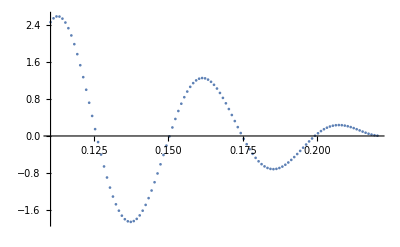

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 45.8294+1.20645×10^-9 ⅈ and 0.0000485624 for the integral and error estimates.

```mathematica
DiscretePlot[NIntegrate[S[delta, b,t]Cos[2π t x],{t,-100,100}],{x,Log[2]/(2π),Log[4]/(2π),0.001},Filling->None,AxesOrigin->None]
```

```mathematica
delta = Log[4]/(2π);
b1 = 21.25; b2 = 18.4;
```

```mathematica
S[d_,b_,z_]:=-1/2(B[d(-b-z)]+B[d(z-b)]);
```

```mathematica
S1[z_]:=-1/2(B[delta(-b1-z)]+B[delta(z-b1)]);
```

```mathematica
S2[z_]:=-1/2(B[delta(-b2-z)]+B[delta(z-b2)]);
```

```mathematica
x=Log[2]/(2π);NIntegrate[S1[t]Cos[2π t x],{t,-100,100}]
```

```mathematica
2.4619899236631975
```

```mathematica
x=Log[2]/(2π);NIntegrate[S2[t]Cos[2π t x],{t,-100,100}]
```

```mathematica
-1.9574965558667388
```

```mathematica
1.9574965558667388/2.4619899236631975
```

0.795087

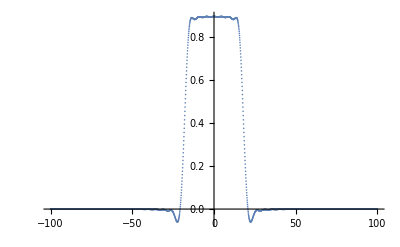

31.2276

```mathematica
0.5044933677964587;

Stot[z_] = 1/2(0.795087151678581S1[z] + S2[z]);

DiscretePlot[Stot[z],{z,-100,100,0.1},Filling->None]
hatStot = 1/2(0.795087151678581(2b1 - (2π)/Log[4]) + (2b2 - (2π)/Log[4]))
```

```mathematica
31.227611244482794

(18.4*2)*1.7951 + 2*(22.25-18.4)
```

31.2276

73.7597

```mathematica
Clear[t]
u=0;Re[NIntegrate[Gamma'[1/4+(ⅈ t)/2+u]/Gamma[1/4+(ⅈ t)/2+u] Stot[t],{t,-10000,10000}]]-hatStot*Log[π]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 34.9317-4.67471×10^-10 ⅈ and 0.0000390417 for the integral and error estimates.

-0.81544

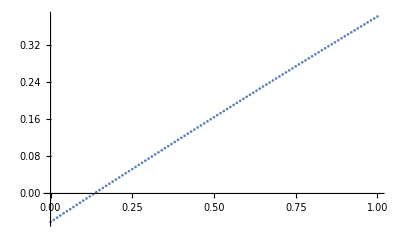

```mathematica
DiscretePlot[Re[NIntegrate[Gamma'[1/4+(ⅈ t)/2+ u]/Gamma[1/4+(ⅈ t)/2+ u] Stot[t],{t,-200,200}]]-Log[π]hatStot,{u,0,1,0.01},Filling->None,AxesOrigin->{0,0}]
```

```mathematica
Clear[x,y]
```

```mathematica
Plot3D[Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] Stot[r],{r,-200,200}]]-Log[π]hatStot,{x,0,1},{y,-1,1}]
```

-Graphics3D-

0.680154

```mathematica
LL[n_] :=Log[n]/(2π);
```

```mathematica
Plot3D[Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S[LL[2],22.6,r],{r,-200,200}]]-Log[π](45.2-1/LL[2]),{x,0,2},{y,-20,20}]
```

-Graphics3D-

```mathematica
Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2]/Gamma[1/4+(ⅈ r)/2] S[LL[2],22.6,r],{r,-200,200}]]-Log[π](45.2-1/LL[2])
```

0.395163

```mathematica
Log[π]
```

Log[π]